# Bifurcación transcrítica

## Forma normal:

### Espacio fase

```mathematica
Manipulate[Plot[r*x-x^2,{x,-4,4},PlotRange->{{-4,4},{-1,4}},AxesLabel->{x, OverDot[x]}],{r,-3.5,3.5}]
```

### Diagrama de bifurcación

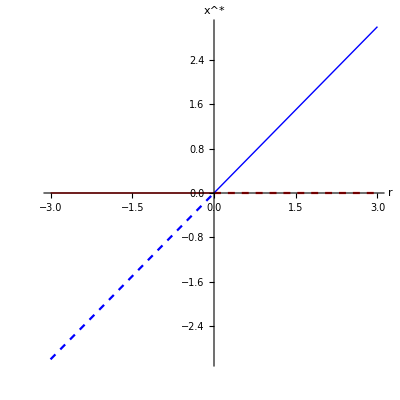

```mathematica
biftn=Show[Plot[0,{r,-3,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Thick},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],Plot[0,{r,0,3},AxesLabel->{r,SuperStar[x]},PlotStyle->{Red,Dashed},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],Plot[r,{r,-3,0},AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Dashed},PlotRange->{{-3,3},{-3,3}},AspectRatio->1],Plot[r,{r,0,3},AxesLabel->{r,SuperStar[x]},PlotStyle->{Blue,Thick},PlotRange->{{-3,3},{-3,3}},AspectRatio->1]]
```

## Ejemplo:

```mathematica
Manipulate[Plot[x-a*(1-Exp[-b*x]),{x,-4,4},PlotRange->{{-4,4},{-1,4}},AxesLabel->{x, OverDot[x]}],{a,-3.5,3.5},{b,-2/3,2/3}]
```

```mathematica
ststex1ust=ParallelTable[{a,x/.FindRoot[x-a*(1-Exp[2*x/3])==0,{x,-4}]},{a,-3.5,-3/2,0.01}];
```

```mathematica
ststex1st=ParallelTable[{a,x/.FindRoot[x-a*(1-Exp[2*x/3])==0,{x,4}]},{a,-3/2,-1/3,0.01}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

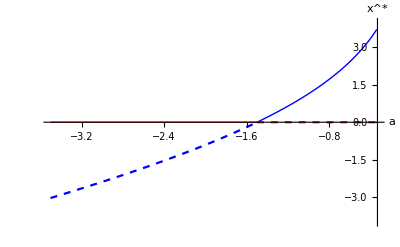

```mathematica
ex1bdiag=Show[ListPlot[ststex1ust,Joined->True,PlotStyle->{Blue,Dashed},AxesLabel->{a,SuperStar[x]},PlotRange->{{-3.5,-1/3},{-4,4}}],ListPlot[ststex1st,Joined->True,PlotStyle->{Blue,Thick},AxesLabel->{a,SuperStar[x]},PlotRange->{{-3.5,-1/3},{-4,4}}],Plot[0,{a,-3.5,-3/2},PlotStyle->{Red,Thick},AxesLabel->{a,SuperStar[x]},PlotRange->{{-3.5,-3/2},{-4,4}}],Plot[0,{a,-3/2,-1/3},PlotStyle->{Red,Dashed},AxesLabel->{a,SuperStar[x]},PlotRange->{{-3.5,-1/3},{-4,4}}]]
```

## Ejemplo:

```mathematica
Manipulate[Plot[r*Log[x]+x-1,{x,0,2},PlotRange->{{0,2},{-1,1}},AxesLabel->{x, OverDot[x]}],{r,-2,0}]
```

```mathematica
ststex2ust=ParallelTable[{r,x/.FindRoot[r*Log[x]+x-1==0,{x,2}]},{r,-1.5,-1,0.01}];
```

```mathematica
ststex2st=ParallelTable[{r,x/.FindRoot[r*Log[x]+x-1==0,{x,0.1}]},{r,-1,-1/2,0.01}];
```

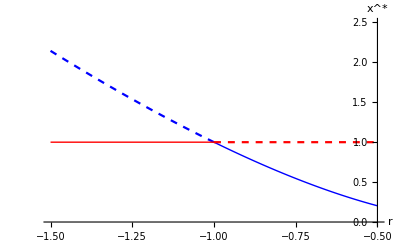

```mathematica
ex2bdiag=Show[ListPlot[ststex2ust,Joined->True,PlotStyle->{Blue,Dashed},AxesLabel->{r,SuperStar[x]},PlotRange->{{-1.5,-1/2},{0,2.5}}],ListPlot[ststex2st,Joined->True,PlotStyle->{Blue,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-1.5,-1/2},{0,2.5}}],Plot[1,{r,-1.5,-1},PlotStyle->{Red,Thick},AxesLabel->{r,SuperStar[x]},PlotRange->{{-1.5,-1/2},{0,2.5}}],Plot[1,{r,-1,-1/2},PlotStyle->{Red,Dashed},AxesLabel->{r,SuperStar[x]},PlotRange->{{-1.5,-1/2},{0,2.5}}]]
```